Wolfram Quantum Team (quantum AT wolfram.com)

Analog quantum processing units (quantum annealers) use continuous variables for optimization tasks, such as finding global minima. Gate-based quantum computers use discrete quantum gates to manipulate qubits for versatile quantum algorithms, including factorization, simulation, and optimization. One example of analog Quantum Processing Units (QPUs) is Aquila, which is a neutral-atom QPU from QuEra Computing, with up to 256 qubit. Aquila is also available on Amazon Braket, which is accessible using AWS service connect from a Wolfram notebook. In this computational essay, we will focus on some examples from QuEra's recent white paper, and do the simulation using quantum functionalities of Wolfram quantum framework, and also show how to send queries to Aquila, using Amazon Braket.

The Hamiltonian for QuEra system of atoms is given by:

where  is the the Rabi frequency,  the laser phase, and  the detuning of the driving laser field coupling the ground states  and excited Rydberg state  of the j-th atom.  represents the van der Waals interaction between atom-j and atom-k, while is  the number operator of j-th site (more info on actual values of C_6 can be found in QuEra webpages).

We have defined the corresponding Hamiltonian as follows: AquilaHamiltonian[sites, {Ω, Δ, ϕ}], where it takes sites as a list of atom positions, {{x_1,y_1},{x_2,y_2},...}, with each position in μm,   is the the Rabi frequency,  the laser phase, and  the detuning of the driving laser field.

## Single atom

Let’s consider the single atom dynamics.

### Rabi Oscillation (Ω=constant, Δ=0 and ϕ=0)

This part is related to Section 2.1 of the QuEra white paper.

For this case, one can get the state symbolically.

```mathematica
ψ1RO=QuantumEvolve[AquilaHamiltonian[{{0,0}},{15.,0,0}],t];
```

As an example, calculate the populations at t=1μs

```mathematica
ψ1RO[1.]["Probability"]
```

<|0→0.120156,1→0.879844|>

Population of ground state as a function of time:

```mathematica
Plot[ψ1RO["Probability"][[1]],{t,0,1},FrameLabel->{"t_f (μs)",(|0"ψ_t_f"|)^2},Frame->True,PlotLabel->"Population of ground state in time"]
```

-Graphics-

The decoherence effect of the environment can be added as a damping effect, with the rate 1/τ, toward the thermal state of ρ=𝕀/2.

```mathematica
prob0[t_,τ_]=(a-1/2)ⅇ^(-t/τ)+1/2/.{a->ψ1RO[t]["Probability"][[1]]};
```

```mathematica
Plot[{ψ1RO["Probability"][[1]],prob0[t,3.6]},{t,0,10},FrameLabel->{"t_f (μs)",(|0"ψ_t_f"|)^2},Frame->True,PlotLabel->"Population of ground state in time",PlotStyle->{Automatic,Directive[Dashed,Red]},PlotLegends->{"No noise","With noise"}]
```

-Graphics-

### Ramsey Protocol (Ω as two pulses, Δ=constant, ϕ=0)

This part is related to Section 2.2 of the QuEra white paper.

For this protocol, the atom is driven by two pulses, with a hold time between pulses, and Δ and ϕ are set to zero.

```mathematica
pulses[{amplitude_,δt_,gap_},t_]:=Piecewise[{{amplitude, 0≤t<=δt||gap≤t<=δt+gap}, {0, True}}];
```

```mathematica
data=Module[{δt=.1,amplitude=12.5,plotRabi,plotProb,state,prob={}},
Table[
state=QuantumEvolve[AquilaHamiltonian[{{0,0}},{pulses[{amplitude,δt,gap},t],10.5,0}],{t,0,4}];
plotRabi=Plot[pulses[{amplitude,δt,gap},t],{t,-δt,2δt+gap},];
prob=Join[prob,{{δt+gap,state[δt+gap]["Probability"][[1]]}}];
plotProb=ListLinePlot[prob,];
{plotRabi,plotProb},{gap,Range[.18,3,.1]}]];
```

```mathematica
ListAnimate[images=GraphicsRow[#,ImageSize->Large]&/@data]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Rabi.gif",images,"DisplayDurations"->.3,AnimationRepetitions->100]
```

/Users/mohammadb/Documents/GitHub/QuantumFramework/Notebooks/Rabi.gif

### Floquet Protocol (Ω=const., Δ=const. Sin[ω t], and ϕ=0)

This part is related to Section 2.2 of the QuEra white paper.

In this scenario, the Rabi drive remains constant, and the detuning oscillates sinusoidally over time, with a phase set to zero.

```mathematica
Plot[{15.,15.Sin[5π t],0},{t,0,4},PlotLegends->{"Ω","Δ","ϕ"}]
```

-Graphics-

```mathematica
ψFlo=QuantumEvolve[AquilaHamiltonian[{{0,0}},{15.,15.Sin[5π t],0}],{t,0,4}];
```

Population per site (keys are site labels (qubits) and values are population):

```mathematica
Plot[ψFlo[t]["Probability"][[1]],{t,0,4},PlotRange->{0,1},FrameLabel->{"t_f (μs)",(|0"ψ_t_f"|)^2},Frame->True,PlotLabel->"Population of ground state in time"]
```

-Graphics-

### Spin echo

This part is related to Section 2.3 of the QuEra white paper.

```mathematica
Ω[{δt_,gap_},t_]:=Piecewise[{{13., 0<=t<=δt||δt+gap<=t<=3δt+gap||3δt+2gap<=t<=4δt+2gap}, {0, True}}];
Δ[{δt_,gap_},t_]:=Piecewise[{{10, 3δt+gap<=t<=3δt+2gap}, {0, True}}];
ϕ[{δt_,gap_},t_]:=Piecewise[{{1.8, gap/2+δt≤t≤(3 gap)/2+3 δt}, {3, (3 gap)/2+3 δt≤t≤2 gap+4 δt}, {0, True}}];
```

```mathematica
δt=.2;
With[{gap=1.3},Plot[{Ω[{δt,gap},t],Δ[{δt,gap},t],ϕ[{δt,gap},t]},{t,-.5,3.5},Exclusions->None,PlotRange->All,PlotPoints->100,PlotLegends->{"Ω","Δ","ϕ"},Filling->{2->Axis}]]
```

-Graphics-

```mathematica
points=Table[{gap,QuantumEvolve[AquilaHamiltonian[{{0.,0.}},{Ω[{δt,gap},t],Δ[{δt,gap},t],ϕ[{δt,gap},t]}],{t,0,5δt+2gap}][5δt+2gap]["Probability"][[1]]},{gap,0,2,.05}];
```

```mathematica
ListLinePlot[points,AxesOrigin->{0,0},PlotRange->{{0,2},{0,1}},Filling->Axis,AspectRatio->1/2]
```

-Graphics-

## Two atoms

### Rydberg blockade radius

This part is related to Section 3.1 of the QuEra white paper.

```mathematica
timePoints={0.,1.,3.,4.};
amplitudeValues={0,15.,15.,0};
detuningValues=30{-1.,-1.,1.,1.};
```

Time-dependent amplitude:

```mathematica
Ω[t_]=Interpolation[Thread[{timePoints,amplitudeValues}],InterpolationOrder->1][t];
```

Time-dependent Hamiltonian detuning:

```mathematica
Δ[t_]=Interpolation[Thread[{timePoints,detuningValues}],InterpolationOrder->1][t];
```

Note that the laser phase (ϕ) is constant and set to zero.

```mathematica
ϕ[t_]=0;
```

Visualize time series:

```mathematica
ts=AssociationThread[{"amplitude", "detuning","phase"},{Ω[t],Δ[t],ϕ[t]}];
GraphicsRow[Plot[ts[#],{t,0,timePoints[[-1]]},Frame->True,Filling->0,FrameLabel->{"time (μs)","rad/s"},PlotRange->Full,AspectRatio->1/2,PlotLabel->#]&/@{"amplitude", "detuning","phase"},ImageSize->1000]
```

-Graphics-

```mathematica
ψ2RB=Table[QuantumEvolve[AquilaHamiltonian[{{0.,0.},{0.,d}},{Ω[t],Δ[t],ϕ[t]}],{t,0,timePoints[[-1]]}],{d,Range[4,10,.1]}];//AbsoluteTiming
```

{88.0199,Null}

```mathematica
prob=AssociationThread[{"00","01","10","11"},Transpose[Values[#[4.]["Probability"]]&/@ψ2RB]];
```

```mathematica
ListLinePlot[Transpose[{Range[4,10,.1],prob["00"]}],PlotLegends->{"P_00 (0 Rydberg)"},PlotRange->All,AspectRatio->1/2]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{Range[4,10,.1],#}]&/@{prob["10"]+prob["01"],prob["11"]},PlotLegends->{"P_01+P_10 (1 Rydberg)","P_11 (2 Rydberg)"},AspectRatio->1/2]
```

-Graphics-

### Levine-Pichler gate analogues

This part is related to Section 3.3 of the QuEra white paper.

```mathematica
Ω[t_]=Piecewise[{{10,0<=t<=.45||0.55<=t<=1},{0,True}}];
```

```mathematica
Δ[t_]=4;
```

```mathematica
ϕ[t_]=3.9UnitStep[t-.5];
```

```mathematica
ts=AssociationThread[{"amplitude", "detuning","phase"},{Ω[t],Δ[t],ϕ[t]}];
GraphicsRow[Plot[ts[#],{t,-.1,timePoints[[-1]]},Frame->True,Filling->0,FrameLabel->{"time (μs)","rad/s"},PlotRange->Full,AspectRatio->1/2,PlotLabel->#,Exclusions->None]&/@{"amplitude", "detuning","phase"},ImageSize->1000]
```

-Graphics-

```mathematica
ψLP=QuantumEvolve[AquilaHamiltonian[{{0.,0.},{0.,4}},{Ω[t],Δ[t],ϕ[t]}],{t,0,2.}];//AbsoluteTiming
```

{2.60055,Null}

```mathematica
data=Transpose[Table[Values[ψLP[t]["Probability"]],{t,0.001,2.,.01}]];
```

```mathematica
ListLinePlot[{#1,#2+#3}&@@data,PlotRange->{0,1},PlotLegends->{"P_00 (0 Rydberg)","P_01+P_10 (1 Rydberg)"}]
```

-Graphics-

```mathematica
ListLinePlot[data[[-1]],PlotLegends->{"P_11 (2 Rydberg)"}]
```

-Graphics-

### Interacting non-equilibrium dynamics of two atoms

This part is related to Section 3.4 of the QuEra white paper.

```mathematica
ψ2NE=QuantumEvolve[AquilaHamiltonian[{{0.,0.},{0.,8.5}},{15,0,0}],{t,0,2.}];//AbsoluteTiming
```

{2.09,Null}

```mathematica
ListLinePlot[{#1,#2+#3,#4}&@@Transpose[Table[Values[ψ2NE[t]["Probability"]],{t,0.001,2.,.05}]],PlotRange->{0,1},PlotLegends->{"P_00 (0 Rydberg)","P_01+P_10 (1 Rydberg)","P_11 (2 Rydberg)"}]
```

-Graphics-

## Multi-atoms: ordered phases

This part is related to Section 4.1 of the QuEra white paper.

```mathematica
time={0,.8,4-.8,4};
omega={0,15.8,15.8,0};
delta={-16.33,-16.33,16.33,16.33};
```

```mathematica
Ω[t_]=Interpolation[Transpose[{time,omega}],InterpolationOrder->1][t];
Δ[t_]=Interpolation[Transpose[{time,delta}],InterpolationOrder->1][t];
ϕ[t_]=0;
```

```mathematica
Plot[{Ω[t],Δ[t],ϕ[t]},{t,0,time[[-1]]},PlotLegends->{"Ω","Δ","ϕ"}]
```

-Graphics-

```mathematica
sitesMA=6.1Table[{i,0},{i,0,10}];
```

```mathematica
ListPlot[MapIndexed[Labeled[#1,Style[#2[[1]],White],{Center,Center},Background->None]&,sitesMA],AspectRatio->1,PlotStyle->PointSize[.05],Frame->True,GridLines->Automatic,FrameLabel->{"Position (μm)","Position (μm)"},PlotLabel->"Atoms's position in a 3x3 lattice"]
```

-Graphics-

```mathematica
ψMA=QuantumEvolve[AquilaHamiltonian[sitesMA,{Ω[t],Δ[t],ϕ[t]}],{t,0,time[[-1]]}];//AbsoluteTiming
```

{143.696,Null}

```mathematica
With[{data=Sort[ψMA[time[[-1]]]["Probability"]][[-10;;]]},BarChart[data,BarOrigin->Left,ChartLabels->(FromDigits[#["Name"]]&/@Keys[data])]]
```

-Graphics-

```mathematica
With[{data=(#[ψMA[time[[-1]]]])["Norm"]&/@Table[QuantumOperator[QuantumState["1"]["Dagger"],{{},{i}}],{i,11}]},BarChart[data,ChartLabels->Range[11]]]
```

-Graphics-

```mathematica
cij[{i_,j_},ψ_]:=If[i==j,QuantumOperator[QuantumState["1"]["Dagger"],{{},{i}}],QuantumOperator[QuantumState["11"]["Dagger"],{{},{i,j}}]][ψ]["Norm"]-(QuantumOperator[QuantumState["1"]["Dagger"],{{},{i}}][ψ]["Norm"])(QuantumOperator[QuantumState["1"]["Dagger"],{{},{j}}][ψ]["Norm"])
```

```mathematica
corrMat=Table[cij[{i,j},ψMA[time[[-1]]]],{i,11},{j,11}];
```

```mathematica
corrMat//MatrixForm
```

-Graphics-

```mathematica
MatrixPlot[corrMat,PlotLegends->Automatic]
```

-Graphics-

## Multi atoms: Blockaded Rabi Oscillations

This part is related to Example 2 from QuEra GiHub.

The Rydberg blockade effect arises from the strong interactions between Rydberg atoms. When two or more Rydberg atoms are in close proximity, the strong interactions between them can prevent multiple atoms from simultaneously being excited to a Rydberg state. In other words, the excitation of one Rydberg atom can “block” the excitation of nearby atoms.

Define positions of atoms in a 2D lattice

```mathematica
pnts[p_,r_,zero_:True]:=With[{data=r Table[{Cos[2 Pi k /p],Sin[2 Pi k /p]},{k,p}]},If[zero,Append[data,{0,0}],data]]
```

```mathematica
sitesRB=pnts[6,4];
```

Plot atoms’s lattice

```mathematica
ListPlot[MapIndexed[Labeled[#1,Style[#2[[1]],White],{Center,Center},Background->None]&,sitesRB],PlotRange->Full,AspectRatio->1,PlotStyle->PointSize[.1],Frame->True,GridLines->Automatic,FrameLabel->{"Position (μm)","Position (μm)"},PlotLabel->"Atoms's position in the lattice with the distance of 4μm"]
```

-Graphics-

Find the final quantum state vector, and wrap it around by a QuantumState:

```mathematica
ψRB=QuantumEvolve[AquilaHamiltonian[sitesRB,{5.,0,0}],{t,0,1.1}];//AbsoluteTiming
```

{32.2953,Null}

```mathematica
ListLinePlot[Table[{t,ψRB[t]["Probability"][[1]]},{t,0,1.1,.05}],AxesLabel->{"μs","P_00"},PlotLabel->"Probability of ground state over time"]
```

-Graphics-

## Multi atoms: quantum scars

This part is related to Section 5 of the QuEra white paper.

```mathematica
time={0,.3,1.9,2.2,2.4,3.8,4};
omega={0,15.7,15.7,0,15.7,15.7,0};
delta={-18.8,-18.8,16.3,16.3,0,0,0};
```

```mathematica
Ω[t_]=Interpolation[Transpose[{time,omega}],InterpolationOrder->1][t];
Δ[t_]=Interpolation[Transpose[{time,delta}],InterpolationOrder->1][t];
ϕ[t_]=0;
```

```mathematica
Plot[{Ω[t],Δ[t],ϕ[t]},{t,0,time[[-1]]},PlotLegends->{"Ω","Δ","ϕ"}]
```

-Graphics-

```mathematica
sitesQS=6.1Table[{i,0},{i,0,12}];
```

```mathematica
ListPlot[MapIndexed[Labeled[#1,Style[#2[[1]],White],{Center,Center},Background->None]&,sitesQS],PlotRange->{-.1,.1},AspectRatio->1/2,PlotStyle->PointSize[.05],Frame->True,GridLines->Automatic,FrameLabel->{"Position (μm)","Position (μm)"},PlotLabel->"Atoms's position in the lattice with the distance of 6.1μm"]
```

-Graphics-

```mathematica
ψQS=QuantumEvolve[AquilaHamiltonian[sitesQS,{Ω[t],Δ[t],ϕ[t]}],{t,0,time[[-1]]}];//AbsoluteTiming
```

{675.778,Null}

Calculate the probability of Néel state 1010101010101 in time:

```mathematica
probNeel=Table[{t,QuantumOperator[QuantumState["1010101010101"]["Dagger"],{{},Range[13]}][ψQS]["Norm"]^2},{t,0,time[[-1]],.1}];
```

Plot it over time:

```mathematica
ListLinePlot[probNeel,PlotRange->{0,1},PlotLabel->"Probability of state 1010101010101 over time",AxesLabel->{"μs","P_1010101010101"}]
```

-Graphics-

```mathematica
projectors=Table[QuantumOperator[QuantumState["1"]["Dagger"],{{},{i}}],{i,13}];
```

```mathematica
sitesOverTime=Table[ψQS["Probabilities"].Tuples[{0,1},Length[sitesQS]],{t,0,time[[-1]],.1}];
```

```mathematica
MatrixPlot[Transpose@sitesOverTime,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListLinePlot[Mean@Transpose[sitesOverTime],PlotLabel->"Rydberg population over time (μs)"]
```

-Graphics-

## Maximum independent set on unit disk graphs

This part is related to Section 6 of the QuEra white paper.

Let’s first analyze the Maximum independent set on unit disk graphs, classically.

Create a King’s graph with a 30% random dropout:

```mathematica
SeedRandom[1337];
kingGraph=VertexDelete[#,RandomSample[VertexList[#],Round[.3VertexCount[#]]],VertexCoordinates->AssociationThread[VertexList[#],GraphEmbedding[#]]]&@DiskGraph[4];
```

Show the King’s graph:

```mathematica
labels=Thread[VertexList[kingGraph]->Range[Length@VertexList[kingGraph]]];
Graph[kingGraph,VertexLabels->labels]
```

-Graphics-

Find an independent vertex set of the King’s graph with a maximum number of vertices:

```mathematica
mis=Lookup[labels,#]&/@FindIndependentVertexSet[kingGraph,Infinity,All]
```

{{2,4,9,11},{2,4,9,10},{2,4,8,9},{2,4,7,11},{2,4,7,8},{2,4,6,11},{2,4,6,10},{2,4,6,8},{1,5,9,11},{1,5,9,10},{1,5,6,11},{1,5,6,10},{1,4,9,11},{1,4,9,10},{1,4,8,9},{1,4,7,11},{1,4,7,8},{1,4,6,11},{1,4,6,10},{1,4,6,8},{1,3,9,11},{1,3,9,10},{1,3,8,9},{1,3,7,11},{1,3,7,8},{1,3,6,11},{1,3,6,10},{1,3,6,8}}

Highlight them in the graph:

```mathematica
ListAnimate[Table[HighlightGraph[kingGraph,VertexList[kingGraph][[i]],VertexLabels->labels,PlotLabel->i],{i,mis}]]
```

-Graphics-

Now, using a quantum algorithm, we will try to find those max independent vertices (in our case, it will be qubits 1, 3, 7 and 8, in a quantum system with 11 qubits).

Create the corresponding 2D lattice, with the distance of 5μm

```mathematica
sitesKG=5.VertexList[kingGraph];
```

Create the corresponding parameters of the Hamiltonian and plot them:

```mathematica
tRampUp=0.3;tRampDown=0.3;tSweep=1.6;OmegaMax=15;DeltaStart=-30;DeltaEnd=80;
tf=tRampUp+tRampDown+tSweep;
```

```mathematica
Plot[#,{t,0,tf},PlotRange->All]&/@AdiabaticDrive[tRampUp,tRampDown,tSweep,OmegaMax,DeltaStart,DeltaEnd]
```

-Graphics-

Find the time-dependent quantum state:

```mathematica
ψMIS=QuantumEvolve[AquilaHamiltonian[sitesKG,AdiabaticDrive[tRampUp,tRampDown,tSweep,OmegaMax,DeltaStart,DeltaEnd]],{t,0,tf},MaxSteps->Infinity];//AbsoluteTiming
```

{139.269,Null}

Final Rydberg population per site at a given time:

```mathematica
RydbergPopulation[t_]:=ψMIS[t]["Probabilities"].Tuples[{0,1},Length[sitesKG]];
```

Plot Rydberg population per sites over time:

```mathematica
ListLinePlot[Transpose@Table[RydbergPopulation[t],{t,0,tf,0.1}],PlotLegends->Range[Length@sitesKG],AxesLabel->{"μs","Rydberg population"},PlotMarkers->Automatic]
```

-Graphics-

Final Rydberg population

```mathematica
BarChart[RydbergPopulation[tf],ChartLabels->Range[Length[sitesKG]]]
```

-Graphics-

Note an independent vertex set is a maximal set of vertices that are never incident to the same edge. Therefore, only picking sites (ie vertices) with high probabilities does not necessary provide the expected solution. For example, as one can see, in the example we studied, there is an edge between site 5 and 7.

Set vertex size by corresponding Rydberg population, and highlight the edge between sites with large-enough population:

```mathematica
Graph[kingGraph,VertexSize->Thread[VertexList[kingGraph]->Log[1+RydbergPopulation[tf]]],VertexLabels->labels,EdgeStyle->{VertexList[kingGraph][[5]]<->VertexList[kingGraph][[7]]->Directive[Thick,Red]}]
```

-Graphics-

Let’s calculate if all maximal independent sets have high probability in quantum version. To do so, we will multiply their Rydberg population as a measure. If quantum algorithm works fine, then the measure for that set should be close to one (or high enough). If not, then it means we won’t be able to find some solutions.

Using classical results, visualize what maximal independent sets are more likely to be obtained from quantum algorithm:

```mathematica
With[{probF=RydbergPopulation[tf]},BarChart[Times@@@(probF[[#]]&/@mis),BarOrigin->Left,ChartLabels->(ToString/@mis),AspectRatio->1/2]]
```

-Graphics-

As one can see, not all of them will be obtained through quantum version. One resolution can be obtained classically, by sampling from sites based on their weights, and pick only those sets with no edge.

```mathematica
trySolution[graph_,proba_,n_]:=With[{idx=RandomSample[proba->Range[Length[proba]],n]},If[EdgeCount[Subgraph[graph,VertexList[graph][[idx]]]]>0,False,Sort@idx]]
```

Try weighted sampling 10 times, return False if any edge between them:

```mathematica
Table[trySolution[kingGraph,RydbergPopulation[tf],4],10]
```

{False,False,False,{9,1,11,4},{4,1,9,11},False,False,False,False,{9,4,11,1}}

## AWS

In this section, we will send a query to QuEra Aquila, using Amazon Braket.

```mathematica
timePoints={0,.25,2.75,3.};
amplitudeMin=0;
amplitudeMax=15.7;
detuningMin=-55.;
detuningMax=55.;
amplitudeValues={amplitudeMin,amplitudeMax,amplitudeMax,amplitudeMin};
phaseValues={0,0,0,0};
detuningValues={detuningMin,detuningMin,detuningMax,detuningMax};
```

```mathematica
ts=TemporalData[TimeSeries@{Thread[{timePoints 10^-6(* μs *),# 10^6 (* MHz *)}]}&/@{amplitudeValues,phaseValues,detuningValues}];
```

```mathematica
DateListPlot[ts,PlotRange->Full,FrameLabel->{"time (μs)","rad/s"},PlotLegends->{"amplitude", "phase", "detuning"},FrameTicks->{Automatic,{Thread[{timePoints 10^-6,ToString/@timePoints}],None}}]
```

-Graphics-

```mathematica
sitesAD=Flatten[Table[6.7{i,j},{i,0,2},{j,0,2}],1];
ListPlot[sitesAD,PlotStyle->PointSize->Large,Frame->True]
```

-Graphics-

```mathematica
ahsProgram=BraketAHS[sitesAD 10^-6(* μm *),{ts}]
```

<|braketSchemaHeader→<|name→braket.ir.ahs.program,version→1|>,setup→<|ahs_register→<|sites→{{0.,0.},{0.,6.7×10^-6},{0.,0.0000134},{6.7×10^-6,0.},{6.7×10^-6,6.7×10^-6},{6.7×10^-6,0.0000134},{0.0000134,0.},{0.0000134,6.7×10^-6},{0.0000134,0.0000134}},filling→{1,1,1,1,1,1,1,1,1}|>|>,hamiltonian→<|drivingFields→{<|amplitude→<|time_series→<|times→{0.,2.5×10^-7,2.75×10^-6,3.×10^-6},values→{0,1.57×10^7,1.57×10^7,0}|>,pattern→uniform|>,phase→<|time_series→<|times→{0.,2.5×10^-7,2.75×10^-6,3.×10^-6},values→{0,0,0,0}|>,pattern→uniform|>,detuning→<|time_series→<|times→{0.,2.5×10^-7,2.75×10^-6,3.×10^-6},values→{-5.5×10^7,-5.5×10^7,5.5×10^7,5.5×10^7}|>,pattern→uniform|>|>},shiftingFields→{}|>|>

```mathematica
braket=ServiceExecute["AWS","GetService",{"Name"->"Braket"}]
```

ServiceObject[…]

```mathematica
devices=braket["SearchDevices",{"Filters"->{},"RequestRegion"->"us-east-1"}]
```

-Graphics-

```mathematica
aquila=devices["Devices",SelectFirst[#DeviceName=="Aquila"&],MapAt[ImportString[#,"RawJSON"]&,"DeviceCapabilities"]]
```

-Graphics-

Send the job to QuEra Aquila:

```mathematica
taskAquila=braket["CreateQuantumTask",
"DeviceArn"->aquila["DeviceArn"],
"DeviceParameters"->{},
"OutputS3Bucket"->"amazon-braket-wolfram-mads",
"OutputS3KeyPrefix"->"tasks",
"Shots"->1000,
"Action"->ahsProgram,
"ValidateRequest"->False,
"RequestRegion"->"us-east-1"
]
```

-Graphics-

```mathematica
outputPath=braket["GetQuantumTask","QuantumTaskArn"->taskAquila["QuantumTaskArn"],"RequestRegion"->"us-east-1"]["OutputS3Directory"]
```

tasks/0dba0554-1751-44db-b650-d1b03bb7a79d

```mathematica
s3=ServiceExecute["AWS","GetService",{"Name"->"S3"}]
```

ServiceObject[…]

```mathematica
aquilaResults=ImportByteArray[s3["GetObject","Bucket"->"amazon-braket-wolfram-mads","Key"->FileNameJoin[{outputPath,"results.json"}],"RequestRegion"->"us-east-1"]["Body"],"RawJSON"];
```

```mathematica
aquilaRydbergPopulation=AssociationThread[Range[9], 1-Total/@Transpose[aquilaResults["measurements"][[All,-1,-1]]]/1000.]
```

<|1→0.928,2→0.043,3→0.927,4→0.032,5→0.898,6→0.031,7→0.92,8→0.023,9→0.933|>

```mathematica
ψAquila=QuantumEvolve[AquilaHamiltonian[sitesAD,AdiabaticDrive[.25,.25,2.5,15.7,-55,55]],{t,0,3}];//AbsoluteTiming
```

{22.8039,Null}

```mathematica
quantumRydbergPopulation=AssociationThread[Range[Length[sitesAD]]->ψAquila[3.]["Probabilities"].Tuples[{0,1},Length[sitesAD]]]
```

<|1→0.978323,2→0.00881876,3→0.978323,4→0.00881876,5→0.985754,6→0.00881876,7→0.978323,8→0.00881876,9→0.978323|>

Different of population between theory and experimental values for each site

```mathematica
BarChart[Merge[{quantumRydbergPopulation,aquilaRydbergPopulation},Identity],ChartLabels->{Range[9],None},ChartLegends->{"Wolfram quantum framework (quantum predictions)","QuEra Aquila"}]
```

-Graphics-

## Initialization

Install quantum paclet:

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall -> True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

Function to generate Analog Hamiltonian Simulation (AHS) for Braket:

```mathematica
ClearAll[BraketAHS];
BraketAHS[
	sites_ /; MatrixQ[sites, NumericQ] && MatchQ[Dimensions[sites], {_, 2}],
	drivingFields : {__TemporalData} /; AllTrue[drivingFields, #["PathCount"] === 3 &],
	shiftingFields : _TemporalData | None : None
] := <|
	"braketSchemaHeader" -> <|"name" -> "braket.ir.ahs.program", "version" -> "1"|>,
	"setup" -> <|
		"ahs_register" -> <|
			"sites" -> sites, "filling" -> ConstantArray[1, Length[sites]]
		|>
	|>,
	"hamiltonian" -> <|
		"drivingFields" -> Map[
			AssociationThread[
				{"amplitude", "phase", "detuning"},
				<|"time_series" -> <|"times" -> #[[All, 1]], "values" -> #[[All, 2]]|>, "pattern" -> "uniform"|> & /@ #["Paths"]
			] &,
			drivingFields
		],
		"shiftingFields" -> Replace[shiftingFields, None -> {}]
	|>
|>
```

```mathematica
ClearAll[AquilaHamiltonian];
AquilaHamiltonian[sites_, {Ω_, Δ_, ϕ_}] := Module[{c6, n},
	c6 = 2π 862690 (*c6 in the van der Waals interaction in MHz μm^6*);
	n = Length[sites] (*number of qubits*);

	N @ Sum[
		Ω/2 QuantumOperator[{{0, ⅇ^(ⅈ ϕ)}, {ⅇ^(-ⅈ ϕ), 0}}, {j}] -
		Δ/2 QuantumOperator["I" - "Z", {j}] +
		Sum[
			c6/(4 EuclideanDistance[sites[[j]], sites[[k]]] ^ 6) *
				QuantumOperator["I" - "Z", {j}] @ QuantumOperator["I" - "Z", {k}],
			{k, j + 1, n}
		],
	{j, n}
	]
]
```

```mathematica
AdiabaticDrive // ClearAll
AdiabaticDrive[tRampUp_, tRampDown_, tSweep_, omegaMax_, deltaStart_, deltaEnd_] := Block[{t, Ω, Δ, ϕ},
	Ω = Interpolation[
		Table[
			{t, Piecewise[{{t omegaMax / tRampUp, t < tRampUp}, {omegaMax, tRampUp ≤ t <= tRampUp + tSweep}, {(tRampUp + tSweep + tRampDown - t) omegaMax / tRampDown, tRampUp + tSweep + tRampDown <= t <= tRampUp + tSweep}, {0, True}}]},
			{t, {0, tRampUp, tRampUp + tSweep, tRampUp + tSweep + tRampDown}}
		],
		InterpolationOrder -> 1
	];
	Δ = Interpolation[
		Table[
			{t, Piecewise[{{deltaStart, t < tRampUp}, {deltaStart + (t - tRampUp) (deltaEnd - deltaStart)  / tSweep, tRampUp ≤ t <= tRampUp + tSweep}, {deltaEnd, t > tRampUp + tSweep}}]},
			{t, {0, tRampUp, tRampUp + tSweep, tRampUp + tSweep + tRampDown}}
		],
		InterpolationOrder -> 1
	];
	
	{Ω[t], Δ[t], 0}
]
```

```mathematica
DiskGraph[{m_Integer ? Positive, n_Integer ? Positive}, rad_ : Sqrt[2]] := RelationGraph[0 < EuclideanDistance[##] <= rad &, Tuples[{Range[m], Range[n]}]]
DiskGraph[n_Integer ? Positive, rad_ : Sqrt[2]] := DiskGraph[{n, n}, rad]
```

```mathematica
walkGenerator[ψ_,{ti_,tf_,δt_}]:=Module[{states,coords},
states=Table[ψ[t],{t,ti,tf,δt}];
coords=#["BlochCartesianCoordinates"]&/@states;
Table[Show[states[[t]]["BlochPlot"],ListLinePlot3D[coords[[;;t]]]],{t,Length@states}]];
```

## scratch paper

```mathematica
time={0,.3,1.9,2.2,2.4,3.8,4};
omega={0,15.7,15.7,0,15.7,15.7,0};
delta={-18.8,-18.8,16.3,16.3,0,0,0};
```

```mathematica
Ω[t_]=Interpolation[Transpose[{time,omega}],InterpolationOrder->1][t];
Δ[t_]=Interpolation[Transpose[{time,delta}],InterpolationOrder->1][t];
ϕ[t_]=0;
```

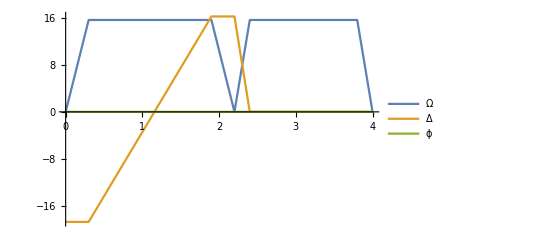

```mathematica
Plot[{Ω[t],Δ[t],ϕ[t]},{t,0,time[[-1]]},PlotLegends->{"Ω","Δ","ϕ"}]
```

```mathematica
sites=6.1Table[i,{i,0,12}];
ψFig51=QuantumEvolve[hamiltonian[sites,{Ω[t],Δ[t],ϕ[t]}],{t,0,time[[-1]]}];
```

```mathematica
prob=Table[{t,QuantumOperator[QuantumState["1010101010101"]["Dagger"],{{},Range[13]}][ψFig51]["Norm"]^2},{t,0,time[[-1]],.1}];
```

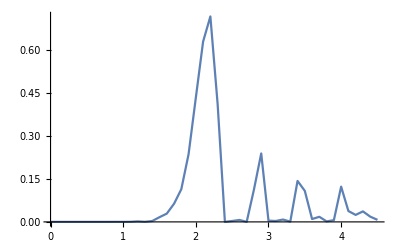

```mathematica
ListLinePlot[prob,PlotRange->All]
```

```mathematica
projectors=Table[QuantumOperator[QuantumState["1"]["Dagger"],{{},{i}}],{i,13}];
```

```mathematica
dt=Table[(#[ψFig51])["Norm"]^2&/@projectors,{t,0,time[[-1]],.1}];
```

```mathematica
Dimensions[dt]
```

{46,13}

```mathematica
ResourceFunction["AddMatplotlibColors"][]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

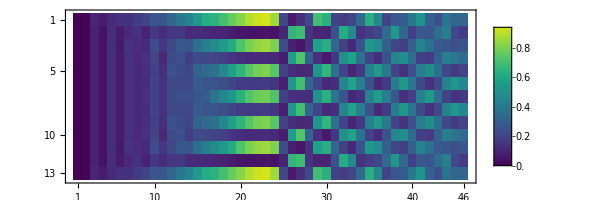

```mathematica
MatrixPlot[Transpose@dt,PlotLegends->Automatic,ColorFunction->"Viridis",ColorFunctionScaling->False]
```

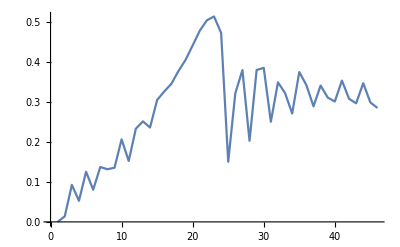

```mathematica
ListLinePlot[Mean@Transpose[dt]]
```

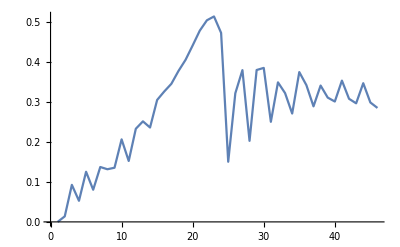

```mathematica
ListLinePlot[Mean@Transpose@Table[Mean@WeightedData[Tuples[{0,1},13],Abs[Normal[ψFig51["State"]]]^2],{t,0,4.5,.1}]]
```

```mathematica
s=QuantumState[{"RandomPure",2}];
```

```mathematica
Mean@WeightedData[Tuples[{0,1},2],Abs[Normal[s["State"]]]^2]
```

{0.569585,0.708018}

```mathematica
QuantumOperator[QuantumState["1"]["Dagger"],{{},{1}}][s]["Norm"]^2
```

0.569585

```mathematica
Subscript[a, #]&/@StringJoin@@@Tuples[{"0","1"},3]
```

{a_000,a_001,a_010,a_011,a_100,a_101,a_110,a_111}

```mathematica
Subscript[a, #]&/@StringJoin@@@Tuples[{"0","1"},4]
```

{a_0000,a_0001,a_0010,a_0011,a_0100,a_0101,a_0110,a_0111,a_1000,a_1001,a_1010,a_1011,a_1100,a_1101,a_1110,a_1111}

```mathematica
With[{n=4},Mean@WeightedData[Tuples[{0,1},4],Subscript[a, #]&/@StringJoin@@@Tuples[{"0","1"},4]]]
```

{(a_1000+a_1001+a_1010+a_1011+a_1100+a_1101+a_1110+a_1111)/(a_0000+a_0001+a_0010+a_0011+a_0100+a_0101+a_0110+a_0111+a_1000+a_1001+a_1010+a_1011+a_1100+a_1101+a_1110+a_1111),(a_0100+a_0101+a_0110+a_0111+a_1100+a_1101+a_1110+a_1111)/(a_0000+a_0001+a_0010+a_0011+a_0100+a_0101+a_0110+a_0111+a_1000+a_1001+a_1010+a_1011+a_1100+a_1101+a_1110+a_1111),(a_0010+a_0011+a_0110+a_0111+a_1010+a_1011+a_1110+a_1111)/(a_0000+a_0001+a_0010+a_0011+a_0100+a_0101+a_0110+a_0111+a_1000+a_1001+a_1010+a_1011+a_1100+a_1101+a_1110+a_1111),(a_0001+a_0011+a_0101+a_0111+a_1001+a_1011+a_1101+a_1111)/(a_0000+a_0001+a_0010+a_0011+a_0100+a_0101+a_0110+a_0111+a_1000+a_1001+a_1010+a_1011+a_1100+a_1101+a_1110+a_1111)}